```mathematica
Subscript[f, 𝒩_][x_]:= (Sin[𝒩 x/2]/Sin[x/2])^2
```

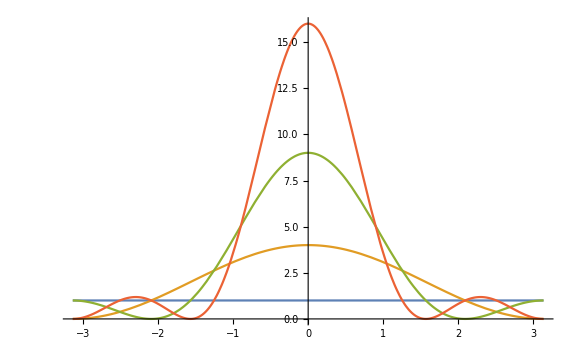

```mathematica
Plot[Table[Subscript[f, 𝒩][x], {𝒩,1,4}]//Evaluate, {x, -π, π}, {ImageSize-> Large, PlotRange-> All}]
```

```mathematica
$Assumptions={{𝒩,a,b}∈Integers};
```

```mathematica
Integrate[Subscript[f, 𝒩][τ], {τ, a, b}]
```

ConditionalExpression[1/(2 (-1+𝒩^2))ⅇ^(-ⅈ a 𝒩-ⅈ b 𝒩) (ⅇ^(ⅈ b 𝒩) Cot[a/2]-2 ⅇ^(ⅈ a 𝒩+ⅈ b 𝒩) Cot[a/2]+ⅇ^(2 ⅈ a 𝒩+ⅈ b 𝒩) Cot[a/2]-ⅇ^(ⅈ b 𝒩) 𝒩^2 Cot[a/2]+2 ⅇ^(ⅈ a 𝒩+ⅈ b 𝒩) 𝒩^2 Cot[a/2]-ⅇ^(2 ⅈ a 𝒩+ⅈ b 𝒩) 𝒩^2 Cot[a/2]-ⅇ^(ⅈ a 𝒩) Cot[b/2]+2 ⅇ^(ⅈ a 𝒩+ⅈ b 𝒩) Cot[b/2]-ⅇ^(ⅈ a 𝒩+2 ⅈ b 𝒩) Cot[b/2]+ⅇ^(ⅈ a 𝒩) 𝒩^2 Cot[b/2]-2 ⅇ^(ⅈ a 𝒩+ⅈ b 𝒩) 𝒩^2 Cot[b/2]+ⅇ^(ⅈ a 𝒩+2 ⅈ b 𝒩) 𝒩^2 Cot[b/2]-ⅈ ⅇ^(ⅈ a+ⅈ b 𝒩) 𝒩 Hypergeometric2F1[1,1-𝒩,2-𝒩,ⅇ^(ⅈ a)]-ⅈ ⅇ^(ⅈ a+ⅈ b 𝒩) 𝒩^2 Hypergeometric2F1[1,1-𝒩,2-𝒩,ⅇ^(ⅈ a)]+ⅈ ⅇ^(ⅈ b+ⅈ a 𝒩) 𝒩 Hypergeometric2F1[1,1-𝒩,2-𝒩,ⅇ^(ⅈ b)]+ⅈ ⅇ^(ⅈ b+ⅈ a 𝒩) 𝒩^2 Hypergeometric2F1[1,1-𝒩,2-𝒩,ⅇ^(ⅈ b)]+ⅈ ⅇ^(ⅈ b 𝒩) Hypergeometric2F1[1,-𝒩,1-𝒩,ⅇ^(ⅈ a)]-ⅈ ⅇ^(ⅈ b 𝒩) 𝒩^2 Hypergeometric2F1[1,-𝒩,1-𝒩,ⅇ^(ⅈ a)]-ⅈ ⅇ^(ⅈ a 𝒩) Hypergeometric2F1[1,-𝒩,1-𝒩,ⅇ^(ⅈ b)]+ⅈ ⅇ^(ⅈ a 𝒩) 𝒩^2 Hypergeometric2F1[1,-𝒩,1-𝒩,ⅇ^(ⅈ b)]+ⅈ ⅇ^(2 ⅈ a 𝒩+ⅈ b 𝒩) Hypergeometric2F1[1,𝒩,1+𝒩,ⅇ^(ⅈ a)]-ⅈ ⅇ^(2 ⅈ a 𝒩+ⅈ b 𝒩) 𝒩^2 Hypergeometric2F1[1,𝒩,1+𝒩,ⅇ^(ⅈ a)]-ⅈ ⅇ^(ⅈ a 𝒩+2 ⅈ b 𝒩) Hypergeometric2F1[1,𝒩,1+𝒩,ⅇ^(ⅈ b)]+ⅈ ⅇ^(ⅈ a 𝒩+2 ⅈ b 𝒩) 𝒩^2 Hypergeometric2F1[1,𝒩,1+𝒩,ⅇ^(ⅈ b)]+ⅈ ⅇ^(ⅈ a+2 ⅈ a 𝒩+ⅈ b 𝒩) 𝒩 Hypergeometric2F1[1,1+𝒩,2+𝒩,ⅇ^(ⅈ a)]-ⅈ ⅇ^(ⅈ a+2 ⅈ a 𝒩+ⅈ b 𝒩) 𝒩^2 Hypergeometric2F1[1,1+𝒩,2+𝒩,ⅇ^(ⅈ a)]-ⅈ ⅇ^(ⅈ b+ⅈ a 𝒩+2 ⅈ b 𝒩) 𝒩 Hypergeometric2F1[1,1+𝒩,2+𝒩,ⅇ^(ⅈ b)]+ⅈ ⅇ^(ⅈ b+ⅈ a 𝒩+2 ⅈ b 𝒩) 𝒩^2 Hypergeometric2F1[1,1+𝒩,2+𝒩,ⅇ^(ⅈ b)]),b≥4 π C[1]&&b≥2 π C[2]&&b≥2 π C[3]&&b≥2 π C[4]&&b≥2 π C[5]&&b≥2 π C[6]&&b≥2 π C[7]&&b≥2 π C[8]&&C[1]∈ℤ&&C[2]∈ℤ&&C[3]∈ℤ&&C[4]∈ℤ&&C[5]∈ℤ&&C[6]∈ℤ&&C[7]∈ℤ&&C[8]∈ℤ&&a<2 π C[2]&&a<2 π C[3]&&a<2 π C[4]&&a<2 π C[5]&&a<2 π C[6]&&a<2 π C[7]&&a<2 π C[8]&&a≤4 π C[1]]